# Spatially Adaptive Finite Volume Method For Moment Models

This Mathematica file implements a spatially adaptive finite volume method for moment models. The spatial adaptivity allows the simulation to use a different number of moments (and so different models) in different parts of the domain. Currently, the setting is the following: the domain is divided in 2 subdomains. In the left subdomain, the number of moments (=: ML) is smaller than the number of moments (=: MR) in the right subdomain.

## Simulation setup

```mathematica
(* Choose number of cells in left and right subdomain *)
nxL = 10;
nxR = 10;
n=nxL+nxR;

(* Choose boundaries of the spatial domain *)
x1=-10;
x2=10;

dx=(x2-x1)/(nxL+nxR);

(* Choose number of moments in left and right subdomain *)
momentsLeft=4;
momentsRight=6;
numberOfMomentsDifference=momentsRight-momentsLeft;

(* Choose initial values *)
m0=3;
m1=2;
m2=3;

epsilon=0.1;

momentsBig=2;

momentSmall=epsilon;

initialValuesLeft={m0,m1,m2};
initialValuesRight={m0,m1,m2};

For[i=4,i<=momentsLeft,i++,
initialValuesLeft=Append[initialValuesLeft,momentsBig];
initialValuesRight=Append[initialValuesRight,momentsBig];
];
For[i=momentsLeft+1,i<=momentsRight,i++,
initialValuesRight=Append[initialValuesRight,momentSmall];
];

(* Choose Relaxation time *)
Relaxation=1;

W={};
For[i=0,i<nxL,i++,
values[i]=initialValuesLeft;
W=Join[W,values[i]];
];
values[nxL]=ArrayPad[initialValuesLeft,{0,numberOfMomentsDifference}]; (* Take initial values from the left and add zeroes *)
W=Join[W,values[nxL]];
For[i=1,i<=nxR+1,i++,
values[i+nxL]=initialValuesRight;
W=Join[W,values[i+nxL]];
];

(* Choose time step *)
dt=0.1dx;

time= 0.0;
step=0;

(* Choose end time *)
tend=1.5;
```

## Construction of the spatial discretization matrix

```mathematica
(* Define the model matrices *)
ALeft=SparseArray[{{i_,j_}/;i-j==1:>Sqrt[j],{i_,j_}/;j-i==1:>Sqrt[i]},{momentsLeft,momentsLeft}];
ARight=SparseArray[{{i_,j_}/;i-j==1:>Sqrt[j],{i_,j_}/;j-i==1:>Sqrt[i]},{momentsRight,momentsRight}];
ATilde=ARight;
ATilde[[-numberOfMomentsDifference;;-1,All]]=0;

(* Define the numerical viscosity matrices *)
QLeft=IdentityMatrix[momentsLeft];
QRight=IdentityMatrix[momentsRight];
QTilde=QRight;
QTilde[[-1,All]]=0;

Roe = ConstantArray[0,{n+2,n+2}];
Viscosity=ConstantArray[0,{n+2,n+2}];

(* CREATE THE SPATIAL DISCRETIZATION MATRIX BLOCK BY BLOCK *)

(* First row is a ghost row *)
For[j=1,j<=nxL,j++,
Roe[[1,j]]=ConstantArray[0,{momentsLeft,momentsLeft}];
Viscosity[[1,j]]=ConstantArray[0,{momentsLeft,momentsLeft}];
]

For[j=nxL+1,j<=n+2,j++,
Roe[[1,j]]=ConstantArray[0,{momentsLeft,momentsRight}];
Viscosity[[1,j]]=ConstantArray[0,{momentsLeft,momentsRight}];
]


(* Rows corresponding to moment model of order ML *)
For[i=2,i<nxL,i++,
Roe[[i,i-1]]=ALeft;
Roe[[i,i]]=ConstantArray[0,{momentsLeft,momentsLeft}];
Roe[[i,i+1]]=-ALeft;
Viscosity[[i,i-1]]=-QLeft;
Viscosity[[i,i]]=2*QLeft;
Viscosity[[i,i+1]]=-QLeft;

For[j=1,j<i-1,j++,
Roe[[i,j]]=ConstantArray[0,{momentsLeft,momentsLeft}];
Viscosity[[i,j]]=ConstantArray[0,{momentsLeft,momentsLeft}];
];

For[j=i+2,j<=nxL,j++,
Roe[[i,j]]=ConstantArray[0,{momentsLeft,momentsLeft}];
Viscosity[[i,j]]=ConstantArray[0,{momentsLeft,momentsLeft}];
];

For[j=nxL+1,j<=n+2,j++,
Roe[[i,j]]=ConstantArray[0,{momentsLeft,momentsRight}];
Viscosity[[i,j]]=ConstantArray[0,{momentsLeft,momentsRight}];
];
];

(* Row nxL (corresponds to vector nxL-1 because of the introduced ghost rows *) 
Roe[[nxL,nxL-1]]=ALeft;
Roe[[nxL,nxL]]=ConstantArray[0,{momentsLeft,momentsLeft}];
Roe[[nxL,nxL+1]]=-ArrayPad[ALeft,{{0,0},{0,numberOfMomentsDifference}}];
Viscosity[[nxL,nxL-1]]=-QLeft;
Viscosity[[nxL,nxL]]=2*QLeft;
Viscosity[[nxL,nxL+1]]=-ArrayPad[QLeft,{{0,0},{0,numberOfMomentsDifference}}];

For[j=1,j<nxL-1,j++,
Roe[[nxL,j]]=ConstantArray[0,{momentsLeft,momentsLeft}];
Viscosity[[nxL,j]]=ConstantArray[0,{momentsLeft,momentsLeft}];
];

For[j=nxL+2,j<=n+2,j++,
Roe[[nxL,j]]=ConstantArray[0,{momentsLeft,momentsRight}];
Viscosity[[nxL,j]]=ConstantArray[0,{momentsLeft,momentsRight}];
];


(* Row nxL+1 (correspond to vector nxL because of the introduced  ghost rows *)
Roe[[nxL+1,nxL]]=ArrayPad[ALeft,{{0,numberOfMomentsDifference},{0,0}}];
Roe[[nxL+1,nxL+1]]=ConstantArray[0,{momentsRight,momentsRight}];
Roe[[nxL+1,nxL+2]]=-ATilde;
Viscosity[[nxL+1,nxL]]=-ArrayPad[QLeft,{{0,numberOfMomentsDifference},{0,0}}];
Viscosity[[nxL+1,nxL+1]]=2*ArrayPad[QLeft,{{0,numberOfMomentsDifference},{0,numberOfMomentsDifference}}];
Viscosity[[nxL+1,nxL+2]]=-QTilde;

For[j=1,j<nxL,j++,
Roe[[nxL+1,j]]=ConstantArray[0,{momentsRight,momentsLeft}];
Viscosity[[nxL+1,j]]=ConstantArray[0,{momentsRight,momentsLeft}];
];

For[j=nxL+3,j<=n+2,j++,
Roe[[nxL+1,j]]=ConstantArray[0,{momentsRight,momentsRight}];
Viscosity[[nxL+1,j]]=ConstantArray[0,{momentsRight,momentsRight}];
];

(* Row nxL+2 (corresponds to vector nxL+1 because of the introduced ghost rows *)

Roe[[nxL+2,nxL+1]]=ARight;
Roe[[nxL+2,nxL+1]][[All,-numberOfMomentsDifference;;-1]]=0;
Roe[[nxL+2,nxL+2]]=ConstantArray[0,{momentsRight,momentsRight}];
Roe[[nxL+2,nxL+3]]=-ARight;
Viscosity[[nxL+2,nxL+1]]=-QRight;
Viscosity[[nxL+2,nxL+1]][[All,-numberOfMomentsDifference;;-1]]=0;
Viscosity[[nxL+2,nxL+2]]=2*QRight;
Viscosity[[nxL+2,nxL+3]]=-QRight;


For[j=1,j<=nxL,j++,
Roe[[nxL+2,j]]=ConstantArray[0,{momentsRight,momentsLeft}];
Viscosity[[nxL+2,j]]=ConstantArray[0,{momentsRight,momentsLeft}];
];

For[j=nxL+4,j<=n+2,j++,
Roe[[nxL+2,j]]=ConstantArray[0,{momentsRight,momentsRight}];
Viscosity[[nxL+2,j]]=ConstantArray[0,{momentsRight,momentsRight}];
];


(* Rows corresponding to moment model of order MR (without the last one) *)
For[i=nxL+3,i<n+2,i++,
Roe[[i,i-1]]=ARight;
Roe[[i,i]]=ConstantArray[0,{momentsRight,momentsRight}];
Roe[[i,i+1]]=-ARight;

Viscosity[[i,i-1]]=-QRight;
Viscosity[[i,i]]=2*QRight;
Viscosity[[i,i+1]]=-QRight;

For[j=1,j<=nxL,j++,
Roe[[i,j]]=ConstantArray[0,{momentsRight,momentsLeft}];
Viscosity[[i,j]]=ConstantArray[0,{momentsRight,momentsLeft}];
];

For[j=nxL+1,j<i-1,j++,
Roe[[i,j]]=ConstantArray[0,{momentsRight,momentsRight}];
Viscosity[[i,j]]=ConstantArray[0,{momentsRight,momentsRight}];
];

For[j=i+2,j<=n+2,j++,
Roe[[i,j]]=ConstantArray[0,{momentsRight,momentsRight}];
Viscosity[[i,j]]=ConstantArray[0,{momentsRight,momentsRight}];
];
];


(* Last rows are ghost rows *)
For[j=1,j<=nxL,j++,
Roe[[n+2,j]]=ConstantArray[0,{momentsRight,momentsLeft}];
Viscosity[[n+2,j]]=ConstantArray[0,{momentsRight,momentsLeft}];
];

For[j=nxL+1,j<=n+2,j++,
Roe[[n+2,j]]=ConstantArray[0,{momentsRight,momentsRight}];
Viscosity[[n+2,j]]=ConstantArray[0,{momentsRight,momentsRight}];
];


RoeFlatten = ArrayFlatten[Roe];
ViscosityFlatten = ArrayFlatten[Viscosity];

(* For the RHS source term, we assume a BGK-type operator and we assume that the source term matrix is a diagonal matrix *)

SourceMatrixLeft =SparseArray[{{i_,i_}/;i>=4:>1},{momentsLeft,momentsLeft}];
SourceMatrixRight =SparseArray[{{i_,i_}/;i>=4:>1},{momentsRight,momentsRight}];

SourceMatrix =ConstantArray[0,{n+2,n+2}];

For[i=1,i<=nxL,i++,
For[j=1,j<i,j++,
SourceMatrix[[i,j]]=ConstantArray[0,{momentsLeft,momentsLeft}]
];
SourceMatrix[[i,i]]=SourceMatrixLeft;
For[j=i+1,j<=nxL,j++,
SourceMatrix[[i,j]]=ConstantArray[0,{momentsLeft,momentsLeft}];
];
For[j=nxL+1,j<=n+2,j++,
SourceMatrix[[i,j]]=ConstantArray[0,{momentsLeft,momentsRight}];
];
];

For[i=nxL+1,i<=n+2,i++,
For[j=1,j<=nxL,j++,
SourceMatrix[[i,j]]=ConstantArray[0,{momentsRight,momentsLeft}]
];
For[j=nxL+1,j<i,j++,
SourceMatrix[[i,j]]=ConstantArray[0,{momentsRight,momentsRight}];
];
SourceMatrix[[i,i]]=SourceMatrixRight;
For[j=i+1,j++,j<=n+2,
SourceMatrix[[i,j]]=ConstantArray[0,{momentsRight,momentsRight}];
];
];

SourceTermVectorLeft={0,0,0};
SourceTermVectorRight={0,0,0};

For[i=4,i<=momentsLeft,i++,
SourceTermVectorLeft=Append[SourceTermVectorLeft,1];
SourceTermVectorRight=Append[SourceTermVectorRight,1];
];
For[i=momentsLeft+1,i<=momentsRight,i++,
SourceTermVectorRight=Append[SourceTermVectorRight,1];
];
SourceTermVector={};
For[i=0,i<nxL,i++,
SourceTermVector=Join[SourceTermVector,SourceTermVectorLeft];
];
For[i=nxL,i<=n+1,i++,
SourceTermVector=Join[SourceTermVector,SourceTermVectorRight];
]
(* Obtain source term vector *)
SourceTermVector=-1/Relaxation*SourceTermVector;
SourceTermMatrix=DiagonalMatrix[SourceTermVector];

(* Obtain Exponential of source term vector *)
SourceTermVector=Exp[SourceTermVector*dt];

(* Obtain transport part of spatial discretization matrix from Roe block matrix and viscosity block matrix *)
BigAMatrix=-1.0/(2*dx)*(Roe+Viscosity);
BigAMatrixFlatten = -1.0/(2*dx)*(RoeFlatten+ViscosityFlatten);

M=BigAMatrixFlatten;
```

## Simulation

```mathematica
While[time<tend,
(* Compute the values of the point s0 along the path *)
norm=0;
For[i=1,i<=momentsLeft,i++,
norm+=(W[[momentsLeft*nxL+i]]-W[[momentsLeft*nxL+momentsRight+i]])^2;
];
normRemainder=0;
For[i=momentsLeft+1,i<=momentsRight,i++,
normRemainder+=W[[momentsLeft*nxL+momentsRight+i]]^2;
];
If[Sqrt[norm]+Sqrt[normRemainder]==0,s0=0,s0=Sqrt[norm]/(Sqrt[norm]+Sqrt[normRemainder])];

(* s0=0; *)

(* THE SYSTEM MATRIX HERE IS A WEIGHTED SUM OF THE BIGGER MATRIX AND THE SMALLER MATRIX *)


WeightedSumRoe=s0*ATilde+(1-s0)*ARight;
WeightedSumRoe[[All,-numberOfMomentsDifference;;-1]]=0;
WeightedSumViscosity=s0*QTilde+(1-s0)*QRight;
WeightedSumViscosity[[All,-numberOfMomentsDifference;;-1]]=0;
modelDiffA=ATilde-ARight;
modelDiffQ=QTilde-QRight;
modelDiffA[[All,-numberOfMomentsDifference;;-1]]=0;
modelDiffQ[[All,-numberOfMomentsDifference;;-1]]=0;
BigAMatrix[[nxL+2,nxL+1]]= -1/(2*dx)*(WeightedSumRoe-WeightedSumViscosity);
BigAMatrix[[nxL+2,nxL+2]]= -1/(2*dx)*(s0*modelDiffA+2*QRight+s0*(modelDiffQ));
BigAMatrix[[nxL+2,nxL+3]]= -1/(2*dx)*(-ARight-QRight);



(* USING THE BIGGER MATRIX *)
(*
BigAMatrix[[nxL+2,nxL+1]]= -1/(2*dx)*(ARight-QRight);
BigAMatrix[[nxL+2,nxL+2]]= -1/(2*dx)*(2*QRight);
BigAMatrix[[nxL+2,nxL+3]]= -1/(2*dx)*(-ARight-QRight);
*)

(* USING THE SMALLER MATRIX *)
(*
BigAMatrix[[nxL+2,nxL+1]]= -1/(2*dx)*(ArrayPad[ALeft,{{0,numberOfMomentsDifference},{0,numberOfMomentsDifference}}]-ArrayPad[QLeft,{{0,numberOfMomentsDifference},{0,numberOfMomentsDifference}}]);
BigAMatrix[[nxL+2,nxL+2]]= -1/(2*dx)*(2*ArrayPad[QLeft,{{0,numberOfMomentsDifference},{0,numberOfMomentsDifference}}]);
BigAMatrix[[nxL+2,nxL+3]]= -1/(2*dx)*(-ArrayPad[ALeft,{{0,numberOfMomentsDifference},{0,numberOfMomentsDifference}}]-ArrayPad[QLeft,{{0,numberOfMomentsDifference},{0,numberOfMomentsDifference}}]);

*)
BigAMatrixFlatten=ArrayFlatten[BigAMatrix];

(* Transport step *)
W=W+dt*BigAMatrixFlatten.W;

(* Relaxation step *)
W=DiagonalMatrix[SourceTermVector].W;

time = time+dt;
step++;
]
```

## Numerical data post processing

```mathematica
(* Collect values that correspond to the same moments *)
```

```mathematica
moments=Table[moment[i],{i,0,momentsRight-1}];
For[i=0,i<momentsRight,i++,moment[i]={}];

For[i=0,i<nxL,i++,
For[j=0,j<momentsRight-numberOfMomentsDifference,j++,
moment[j]=Append[moment[j],W[[momentsLeft*i+j+1]]]
]
]
For[i=0,i<=nxR+1,i++,
For[j=0,j<momentsRight,j++,
moment[j]=Append[moment[j],W[[momentsLeft*nxL+momentsRight*i+j+1]]]
]
]
```

## Plotting

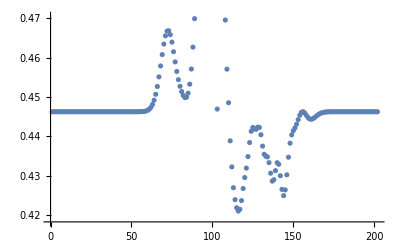

```mathematica
ListPlot[moment[3]]
```

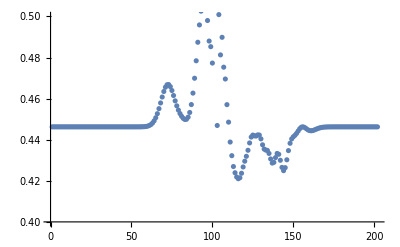

```mathematica
ListPlot[moment[3],PlotRange->{0.4,0.5}]
```

## Stability analysis

### Eigenvalues of the full spatial discretization matrix

```mathematica
(* Obtain the full spatial discretization matrix *)

StabilityMatrix = BigAMatrixFlatten+SourceTermMatrix;
```

```mathematica
(* This computes the eigenvalues of the spatial discretization matrix *)
eigenvaluesStabilityMatrix=Eigenvalues[StabilityMatrix];
realPartEigenvalues=Re[eigenvaluesStabilityMatrix];
realPartEigenvaluesSorted=Sort[realPartEigenvalues];
```

```mathematica
(* This computes the eigenvalue with the biggest real part *)
Eigenvalues[StabilityMatrix,1,Method->{"Arnoldi","Criteria"->"RealPart","MaxIterations"->10000}]
```

#### Plotting

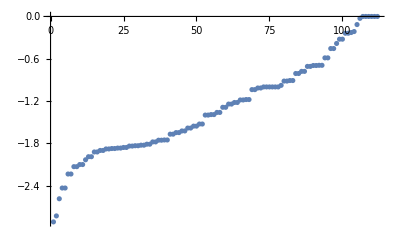

```mathematica
ListPlot[realPartEigenvaluesSorted]
```